```mathematica
Clear[k];k[x_,y_]=Exp[-(x^2+y^2)/4]( 1 + x y )/Sqrt[2Pi]
```

(ⅇ^(1/4 (-x^2-y^2)) (1+x y))/(√(2 π))

```mathematica
Integrate[k[x,x],{x,-Infinity, Infinity}]
```

2

```mathematica
Clear[k2];k2[x_,y_]=FullSimplify[Det[({{k[x,x], k[x,y]}, {k[y,x], k[y,y]}})]]
```

(ⅇ^(-x^2/2-y^2/2) (x-y)^2)/(2 π)

```mathematica
Clear[H];H[t_,a_,b_]=1 - t Integrate[k[x,x],{x,a,b},Assumptions->a>0&&a<b] + (t^2 / 2) Integrate[ k2[x,y],{x,a,b},{y,a,b},Assumptions->a>0&& a < b]
```

1-t ((a ⅇ^(-a^2/2)-b ⅇ^(-b^2/2))/(√(2 π))-Erf[a/(√2)]+Erf[b/(√2)])+1/(4 π)t^2 (-2 ⅇ^(-a^2-b^2) (ⅇ^(a^2/2)-ⅇ^(b^2/2))^2+π Erf[a/(√2)]^2+(a ⅇ^(-a^2/2)-b ⅇ^(-b^2/2)) √(2 π) Erf[b/(√2)]+π Erf[b/(√2)]^2+Erf[a/(√2)] ((-a ⅇ^(-a^2/2)+b ⅇ^(-b^2/2)) √(2 π)-2 π Erf[b/(√2)]))

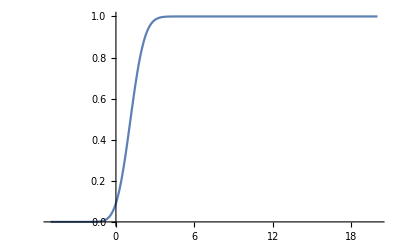

```mathematica
Plot[H[1,a,20],{a,-5,20},PlotRange->{0,1}]
```

```mathematica
FullSimplify[H[1,a,b]]
```

1/(4 π)ⅇ^(-a^2-b^2) (-2 ⅇ^(a^2)+ⅇ^(1/2 (a^2+b^2)) (4+b ⅇ^(a^2/2) √(2 π) (1+Erf[a/(√2)]+Erfc[b/(√2)]))+ⅇ^(b^2) (-2+a ⅇ^(a^2/2) √(2 π) (-2-Erf[a/(√2)]+Erf[b/(√2)])+ⅇ^(a^2) π (1+Erf[a/(√2)]+Erfc[b/(√2)])^2))

```mathematica
problarge[a_]=Limit[%18,b->+Infinity]
```

-(2 ⅇ^(-a^2)-π+a ⅇ^(-a^2/2) √(2 π)+(-2 π+a ⅇ^(-a^2/2) √(2 π)) Erf[a/(√2)]-π Erf[a/(√2)]^2)/(4 π)

```mathematica
densitylarge[a_]=D[problarge[a],a]
```

-1/(4 π)(-4 a ⅇ^(-a^2)+ⅇ^(-a^2/2) √(2 π)-a^2 ⅇ^(-a^2/2) √(2 π)+ⅇ^(-a^2/2) √(2/π) (-2 π+a ⅇ^(-a^2/2) √(2 π))-2 ⅇ^(-a^2/2) √(2 π) Erf[a/(√2)]+(ⅇ^(-a^2/2) √(2 π)-a^2 ⅇ^(-a^2/2) √(2 π)) Erf[a/(√2)])

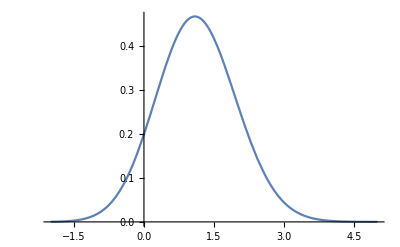

```mathematica
Plot[densitylarge[a],{a,-2,5}]
```

```mathematica
avgnum[a_,b_]=FullSimplify[D[H[t,a,b],t]/.t->0]
```

-1+(-a ⅇ^(-a^2/2)+b ⅇ^(-b^2/2))/(√(2 π))+Erf[a/(√2)]+Erfc[b/(√2)]

```mathematica
Clear[avgdensity];avgdensity[b_]=-D[avgnum[a,b],b]
```

ⅇ^(-b^2/2) √(2/π)-(ⅇ^(-b^2/2)-b^2 ⅇ^(-b^2/2))/(√(2 π))

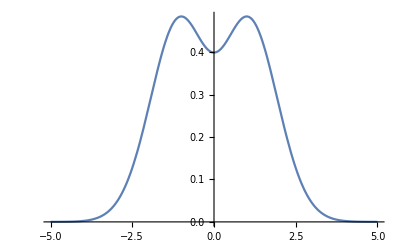

```mathematica
Plot[avgdensity[b],{b,-5,5}]
```

```mathematica
Prob1Eval[a_,b_]=-FullSimplify[(D[H[t,a,b],t])/.t->1]
```

-1/(2 π)ⅇ^(-a^2-b^2) (-2 ⅇ^(a^2)+ⅇ^(1/2 (a^2+b^2)) (4+b ⅇ^(a^2/2) √(2 π) (Erf[a/(√2)]+Erfc[b/(√2)]))+ⅇ^(b^2) (-2+a ⅇ^(a^2/2) √(2 π) (-1-Erf[a/(√2)]+Erf[b/(√2)])+ⅇ^(a^2) π (Erf[a/(√2)]-Erf[b/(√2)]) (1+Erf[a/(√2)]+Erfc[b/(√2)])))

```mathematica
ff[a_,b_]=D[H[t,a,b],t]/.t->0
```

-(a ⅇ^(-a^2/2)-b ⅇ^(-b^2/2))/(√(2 π))+Erf[a/(√2)]-Erf[b/(√2)]

```mathematica
Limit[ff[a,b],a->-Infinity]
```

-1+(b ⅇ^(-b^2/2))/(√(2 π))-Erf[b/(√2)]

```mathematica
D[%,b]
```

-ⅇ^(-b^2/2) √(2/π)+(ⅇ^(-b^2/2))/(√(2 π))-(b^2 ⅇ^(-b^2/2))/(√(2 π))

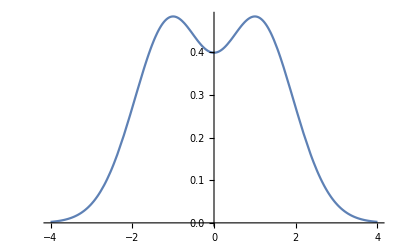

```mathematica
Plot[-%28,{b,-4,4},PlotRange->All]
```

```mathematica
P2[a_,b_]=(1/2)FullSimplify[(D[H[t,a,b],{t,2}])/.t->1]
```

1/(4 π)ⅇ^(-a^2-b^2) (-2 (ⅇ^(a^2/2)-ⅇ^(b^2/2))^2+ⅇ^(1/2 (a^2+b^2)) ((b ⅇ^(a^2/2)-a ⅇ^(b^2/2)) √(2 π)+ⅇ^(1/2 (a^2+b^2)) π (Erf[a/(√2)]-Erf[b/(√2)])) (-1+Erf[a/(√2)]+Erfc[b/(√2)]))

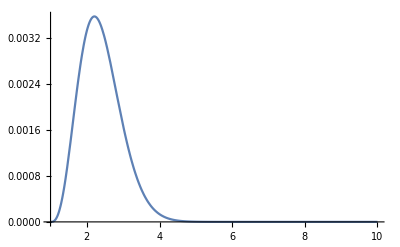

```mathematica
With[{a=1},w[b_]=D[P2[a,b],b];Plot[w[b],{b,a,10}]]
```

```mathematica
Simplify[((D[H[t,a,b],{t,2}])/.t->0) - ((D[H[t,a,b],t])/.t->0)^2 - (D[H[t,a,b],t])/.t->0]
```

-1/2 Erf[a/(√2)]^2+Erf[a/(√2)] (-1+(a ⅇ^(-a^2/2))/(√(2 π))-(b ⅇ^(-b^2/2))/(√(2 π))+Erf[b/(√2)])-1/(2 π)((2+a^2) ⅇ^(-a^2)+(2+b^2) ⅇ^(-b^2)-2 (2+a b) ⅇ^(-a^2/2-b^2/2)-a ⅇ^(-a^2/2) √(2 π)+b ⅇ^(-b^2/2) √(2 π)+(-2 π+(a ⅇ^(-a^2/2)-b ⅇ^(-b^2/2)) √(2 π)) Erf[b/(√2)]+π Erf[b/(√2)]^2)

```mathematica
V[a_,b_]=%
```

-1/2 Erf[a/(√2)]^2+Erf[a/(√2)] (-1+(a ⅇ^(-a^2/2))/(√(2 π))-(b ⅇ^(-b^2/2))/(√(2 π))+Erf[b/(√2)])-1/(2 π)((2+a^2) ⅇ^(-a^2)+(2+b^2) ⅇ^(-b^2)-2 (2+a b) ⅇ^(-a^2/2-b^2/2)-a ⅇ^(-a^2/2) √(2 π)+b ⅇ^(-b^2/2) √(2 π)+(-2 π+(a ⅇ^(-a^2/2)-b ⅇ^(-b^2/2)) √(2 π)) Erf[b/(√2)]+π Erf[b/(√2)]^2)

```mathematica
V[-2,2.]
```

0.236531

```mathematica
NIntegrate[ Exp[- x^2/2] ( 1 + x^2),{x,-2,2}]/Sqrt[2 Pi] - NIntegrate[Exp[-(x^2 + y^2)/2] ((1 + x y)^2),{x,-2,2},{y,-2,2}]/2/Pi
```

0.236531

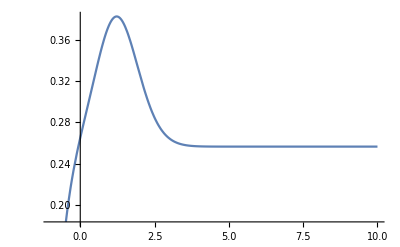

```mathematica
Plot[V[-1,b],{b,-1,10}]
```

```mathematica
ff[-2,2.]
```

-1.69304

```mathematica
Limit[%,a->-Infinity]
```

1/2-(ⅇ^(-b^2))/π-(b ⅇ^(-b^2/2))/(√(2 π))+(1-(b ⅇ^(-b^2/2))/(√(2 π))) Erf[b/(√2)]+1/2 Erf[b/(√2)]^2

```mathematica
Limit[%,b->+Infinity]
```

2

```mathematica
P[x_,n_]:=HermiteH[n, x/Sqrt[2]] / Sqrt[ n! 2^(n) Sqrt[Pi]Sqrt[2]];
```

```mathematica
Integrate[P[x,9]^2 Exp[-x^2/2],{x,-Infinity, Infinity}]
```

1

```mathematica
P[x,0]
```

1/(2 π)^(1/4)

```mathematica
P[x,1]
```

x/(2 π)^(1/4)

```mathematica
Clear[KN];KN[x_,y_,nn_]:=Exp[-(x^2 + y^2)/4]Sum[P[x,j]P[y,j],{j,0,nn-1}]
```

```mathematica
KN[x,y,2]
```

ⅇ^(1/4 (-x^2-y^2)) (1/(√(2 π))+(x y)/(√(2 π)))

```mathematica
KDET2[x_,y_,m_]:=FullSimplify[Det[({{KN[x,x,m], KN[x,y,m]}, {KN[y,x,m], KN[y,y,m]}})]]
```

```mathematica
KDET2[x,y,2]
```

(ⅇ^(-x^2/2-y^2/2) (x-y)^2)/(2 π)

```mathematica
KDET3[x_,y_,z_,m_]:= FullSimplify[Det[({{KN[x,x,m], KN[x,y,m], KN[x,z,m]}, {KN[y,x,m], KN[y,y,m], KN[y,z,m]}, {KN[z,x,m], KN[z,y,m], KN[z,z,m]}})]]
```

```mathematica
KDET3[x,y,z,3]
```

(ⅇ^(1/2 (-x^2-y^2-z^2)) (x-y)^2 (x-z)^2 (y-z)^2)/(4 √2 π^(3/2))

```mathematica
Clear[HN];HN[t_,a_,b_,m_]:=1 - t Integrate[KN[x,x,m],{x,a,b},Assumptions->a<0&& b > 0]+(t^2/2) Integrate[KDET2[x,y,m],{x,a,b},{y,a,b},Assumptions->a<0&& b > 0]- (t^3/(3!))Integrate[KDET3[x,y,z,m],{x,a,b},{y,a,b},{z,a,b},Assumptions->a<0&& b > 0]
```

```mathematica
Clear[H3];H3[t,a,b]=HN[t,a,b,3]
```

1-t ((a (3+a^2) ⅇ^(-a^2/2))/(2 √(2 π))-(b (3+b^2) ⅇ^(-b^2/2))/(2 √(2 π))+3/2 (-Erf[a/(√2)]+Erf[b/(√2)]))+1/(4 π)ⅇ^(-a^2-b^2) t^2 (-3 ⅇ^(a^2)-2 b^2 ⅇ^(a^2)-3 ⅇ^(b^2)-2 a^2 ⅇ^(b^2)+6 ⅇ^(1/2 (a^2+b^2))+2 a^2 ⅇ^(1/2 (a^2+b^2))-a^3 b ⅇ^(1/2 (a^2+b^2))+2 b^2 ⅇ^(1/2 (a^2+b^2))+2 a^2 b^2 ⅇ^(1/2 (a^2+b^2))-a b^3 ⅇ^(1/2 (a^2+b^2))+3 ⅇ^(a^2+b^2) π Erf[a/(√2)]^2+ⅇ^(1/2 (a^2+b^2)) (-3 b ⅇ^(a^2/2)-b^3 ⅇ^(a^2/2)+a (3+a^2) ⅇ^(b^2/2)) √(2 π) Erf[b/(√2)]+3 ⅇ^(a^2+b^2) π Erf[b/(√2)]^2+Erf[a/(√2)] (ⅇ^(1/2 (a^2+b^2)) (3 b ⅇ^(a^2/2)+b^3 ⅇ^(a^2/2)-a (3+a^2) ⅇ^(b^2/2)) √(2 π)-6 ⅇ^(a^2+b^2) π Erf[b/(√2)]))+1/(8 √2 π^(3/2))ⅇ^(-3/2 (a^2+b^2)) t^3 (2 (-b^3 ⅇ^(a^2/2+b^2)+a b^2 (ⅇ^(a^2+b^2/2)+2 ⅇ^(a^2/2+b^2))-a ⅇ^(b^2/2) (-((-1+a^2) ⅇ^(a^2))+ⅇ^(b^2)-2 ⅇ^(1/2 (a^2+b^2)))+b ⅇ^(a^2/2) (ⅇ^(a^2)-(-1+a^2) ⅇ^(b^2)-2 (1+a^2) ⅇ^(1/2 (a^2+b^2))))+√2 ⅇ^(3/2 (a^2+b^2)) π^(3/2) Erf[a/(√2)]^3+ⅇ^(1/2 (a^2+b^2)) ((3+2 b^2) ⅇ^(a^2)+(3+2 a^2) ⅇ^(b^2)+(a^3 b+a b^3-2 a^2 (1+b^2)-2 (3+b^2)) ⅇ^(1/2 (a^2+b^2))) √(2 π) Erf[b/(√2)]+ⅇ^(a^2+b^2) (3 b ⅇ^(a^2/2)+b^3 ⅇ^(a^2/2)-a (3+a^2) ⅇ^(b^2/2)) π Erf[b/(√2)]^2-√2 ⅇ^(3/2 (a^2+b^2)) π^(3/2) Erf[b/(√2)]^3-ⅇ^(a^2+b^2) π Erf[a/(√2)]^2 (-3 b ⅇ^(a^2/2)-b^3 ⅇ^(a^2/2)+a (3+a^2) ⅇ^(b^2/2)+3 ⅇ^(1/2 (a^2+b^2)) √(2 π) Erf[b/(√2)])+Erf[a/(√2)] (-ⅇ^(1/2 (a^2+b^2)) ((3+2 b^2) ⅇ^(a^2)+(3+2 a^2) ⅇ^(b^2)+(a^3 b+a b^3-2 a^2 (1+b^2)-2 (3+b^2)) ⅇ^(1/2 (a^2+b^2))) √(2 π)+2 ⅇ^(a^2+b^2) (-3 b ⅇ^(a^2/2)-b^3 ⅇ^(a^2/2)+a (3+a^2) ⅇ^(b^2/2)) π Erf[b/(√2)]+3 √2 ⅇ^(3/2 (a^2+b^2)) π^(3/2) Erf[b/(√2)]^2))

```mathematica
Clear[P2evals];P2evals[a_,b_]=(D[H3[t,a,b],{t,2}]/.t->1);
```

```mathematica
N[P2evals[0,3]]
```

0.872902

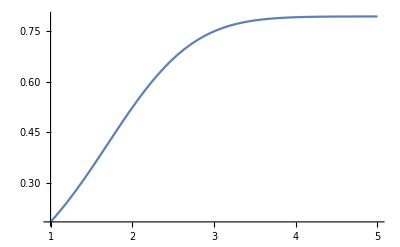

```mathematica
Plot[P2evals[-1,b]/2,{b,1,5}]
```

```mathematica
P2evals[0,b]
```

(ⅇ^(-b^2) (-3-2 b^2+6 ⅇ^(b^2/2)+2 b^2 ⅇ^(b^2/2)-3 ⅇ^(b^2)+(-3 b-b^3) ⅇ^(b^2/2) √(2 π) Erf[b/(√2)]+3 ⅇ^(b^2) π Erf[b/(√2)]^2))/(2 π)+1/(4 √2 π^(3/2))3 ⅇ^(-(3 b^2)/2) (2 (-b^3 ⅇ^(b^2)+b (1-2 ⅇ^(b^2/2)+ⅇ^(b^2)))+ⅇ^(b^2/2) (3+2 b^2-2 (3+b^2) ⅇ^(b^2/2)+3 ⅇ^(b^2)) √(2 π) Erf[b/(√2)]+(3 b+b^3) ⅇ^(b^2) π Erf[b/(√2)]^2-√2 ⅇ^((3 b^2)/2) π^(3/2) Erf[b/(√2)]^3)

```mathematica
NMaximize[{P2evals[a,b],a<b},{a,b}]
```

{1.59367,{a→-0.926709,b→8.56161}}

```mathematica
b/.%365[[2,2]]
```

8.56161

```mathematica
P2evals[a/.%365[[2,1]],b/.%365[[2,2]]]
```

1.59367

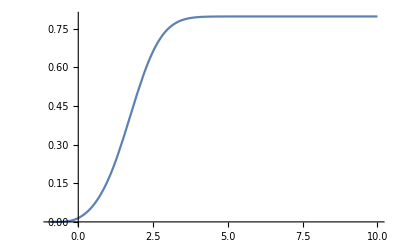

```mathematica
Plot[P2evals[a/.%365[[2,1]],b]/2,{b,a/.%365[[2,1]],10}]
```

```mathematica
P2temp[b_]=P2evals[a/.%365[[2,1]],b];
```

```mathematica
D[P2temp[b],b];
```

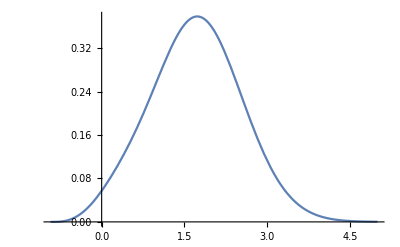

```mathematica
Plot[%384/2,{b,a/.%365[[2,1]],5}]
```

```mathematica
FullSimplify[D[H3[t,a,b],t]/.t->0]
```

1/4 ((-a (3+a^2) ⅇ^(-a^2/2)+b (3+b^2) ⅇ^(-b^2/2)) √(2/π)+6 Erf[a/(√2)]-6 Erf[b/(√2)])

```mathematica
Limit[%,a->-Infinity]
```

1/4 (-6+b (3+b^2) ⅇ^(-b^2/2) √(2/π)-6 Erf[b/(√2)])

```mathematica
D[%,b]
```

1/4 (-6 ⅇ^(-b^2/2) √(2/π)+2 b^2 ⅇ^(-b^2/2) √(2/π)+(3+b^2) ⅇ^(-b^2/2) √(2/π)-b^2 (3+b^2) ⅇ^(-b^2/2) √(2/π))

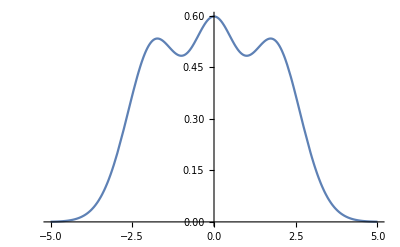

```mathematica
Plot[-%392,{b,-5,5}]
```